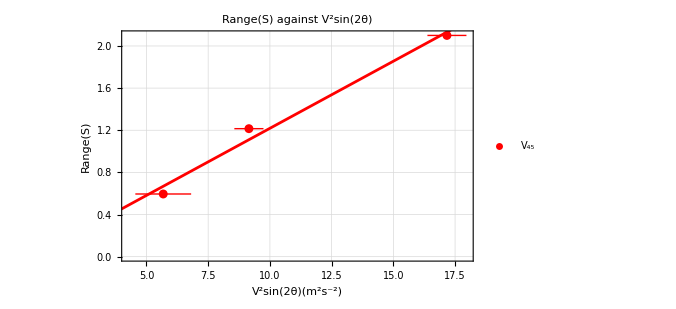
-Graphics-
V_45: y==0.12737 x-0.0552806

```mathematica
(*Define the data*)V45={{5.68,0.595},{9.15,1.215},{17.17,2.1}};

(*error bar*)
V45error={{Around[5.68,1.13],Around[0.595,0.001]},{Around[9.15,0.59],Around[1.215,0.001]},{Around[17.17,0.79],Around[2.1,0.001]}};

(*Extract x and y values for each set of data*)
x1=V45[[All,1]];
y1=V45[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V45,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];

(*Display the equations outside the graph with extended line plot*)
Column[{Show[ListPlot[{V45error},PlotStyle->{Red},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(45\)]\)"}],Plot[{fit1[x]},{x,0,25},PlotStyle->{Red},PlotRange->{{0,25},Automatic}],Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ)(m^2s^-2)","Range(S)"},GridLines->Automatic,PlotLabel->"Range(S) against \!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ)",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(45\)]\): ",eq1}]}]}]
```

```mathematica
1/0.12737005318133
```

7.85114